```mathematica
(* Given coordinates (x, y), generates new coordinates resulting from rotation by angle T *)
rotateSphere[x_,y_,T_]:=N[{Cos[T]*x-Sin[T]*y,Sin[T]*x+Cos[T]*y}];
```

```mathematica
computeX[a_,b_]:=a+Sqrt[4-b^2];
```

```mathematica
(* Initial list of paticles *)
particles={{0,0},{Sqrt[2],Sqrt[2]}};
For[i=1,i<1000,i++;
(* Generate a random angle *)
T=2*Pi*Random[];
(* Rotate entire system in reference frame of T *)
particles=rotateSphere[#[[1]],#[[2]],T]&/@particles;
possibleParticles=Select[particles,Abs[#[[2]]]<2&&#[[1]]≥0&];
newX=Max[computeX[#[[1]],#[[2]]]&/@possibleParticles];
particles=Append[particles,{newX,0}];]
```

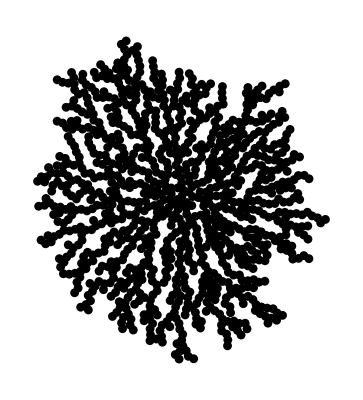

```mathematica
Graphics[{Disk[#, 1.5]&/@particles}]
```

```mathematica
(* Initial list of paticles *)
L=100;
particles={2*#, 0}&/@Range[L/2];
For[i=1,i<1000,i++;
(* Generate a random angle *)
T=L*Random[];
possibleParticles=Select[particles,Abs[(#[[1]]-T)]<2&];
newY=Max[computeX[#[[2]], #[[1]]-T]&/@possibleParticles];
particles=Append[particles,{T,newY}];]
```

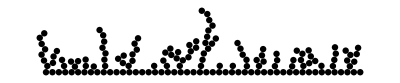

```mathematica
Graphics[{Disk[#, 1]&/@particles}]
```